```mathematica
points = {{0,2.45},{0.05,1.79},{0.1,2.02},{0.15,2.32},{0.2,2.67},{0.33,3.26}};
prime[p_]:= 2/9 + p*(5/9);
pointsprime = Table[{prime[points[[i]][[1]]],points[[i]][[2]]},{i,1,Length[points]}]
pointsprime = {pointsprime,{{2/9,1.35}}}
```

{{2/9,2.45},{0.25,1.79},{0.277778,2.02},{0.305556,2.32},{0.333333,2.67},{0.405556,3.26}}

{{{2/9,2.45},{0.25,1.79},{0.277778,2.02},{0.305556,2.32},{0.333333,2.67},{0.405556,3.26}},{{2/9,1.35}}}

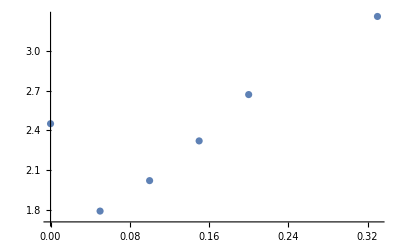

```mathematica
ListPlot[points]
```

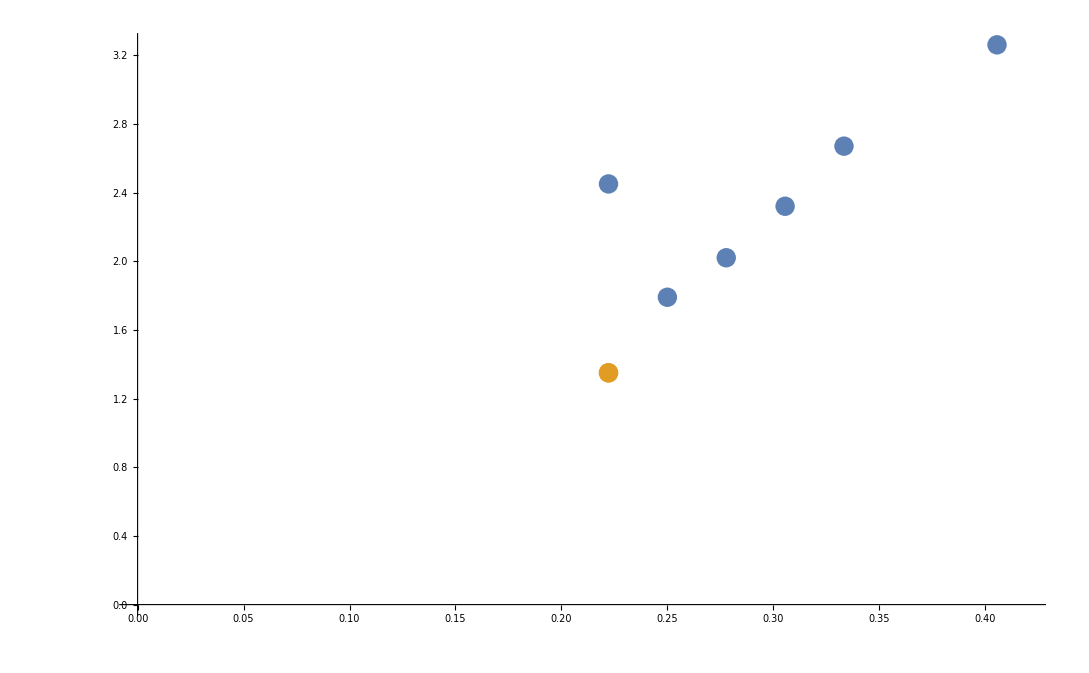

```mathematica
ListPlot[pointsprime, PlotRange->{{0,0.42},{0,Automatic}}]
```

```mathematica
klumperpoints = {{0,Around[2.573,0.0145]},{0.1,Around[2.523,0.0213]},{0.25,Around[2.444,0.017]},{0.3,Around[2.41,0.027]},{1/3,Around[2.374,0.0175]},{0.35,Around[2.394,0.015]},{0.36,Around[2.45,0.0395]},{0.4,Around[3.276,0.082]}};
```

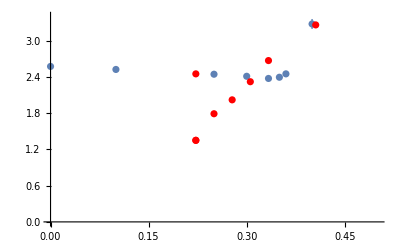

```mathematica
Show[ListPlot[klumperpoints,PlotRange->{{0,0.5},{0,3.4}}],ListPlot[pointsprime,PlotStyle->Red,PlotRange->All]]
```

```mathematica
Around[4,2]
```

4.02.0